```mathematica
(*Q:-Solve the following difeerential equations by using NDSolve.... usin pure function and non-pure function*)
```

InterpolatingFunction[{{0.,20.}},<>][x]

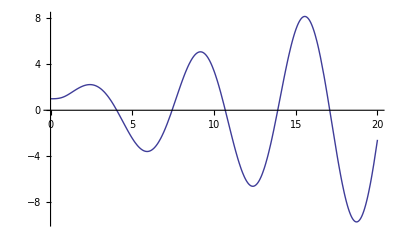

```mathematica
(*1*)
(*non-pure function*)
deq1=y''[x]-(1-x^6)/(1+x^6)Tanh[x]y[x]==Sin[x];
nsol1=NDSolve[{deq1,y[0]==1,y'[0]==0},y[x],{x,0,20}];
nsol1=y[x]/.nsol1[[1]]
Plot[nsol1,{x,0,20}]
```

```mathematica
(*pure function*)
deq1=y''[x]-(1-x^6)/(1+x^6)Tanh[x]y[x]==Sin[x];
nsol1=NDSolve[{deq1,y[0]==1,y'[0]==0},y,{x,0,20}];
nsol1=y[x]/.nsol1[[1]]
Plot[nsol1,{x,0,20}]
```

InterpolatingFunction[{{0.,20.}},<>][x]

-Graphics-

```mathematica
(*Q2:-The differential equation for a forced pendulum is given by θ''[t]+g/l Sin[θ[t]]==f[t] where f[t] is a forcing function.The initial conditions are θ[0]==0 and θ'[0]==0.Compute the following results:
(a):-Solve the differential equation when the forcing function is f[t]=8Exp[-t/5]Sin[5t],g=l=9.8,(b):-Solve the Linearized differential equation*)
(*a*)
g=l=9.8;f[t]=8Exp[-t/5]Sin[5t];deq2=θ''[t]+g/l Sin[θ[t]]==f[t];
nsol2=NDSolve[{deq2,θ[0]==0,θ'[0]==0},θ,{t,0,30}];
nlnsol2=θ[t]/.nsol2[[1]]
```

InterpolatingFunction[{{0.,30.}},<>][t]

```mathematica
(*b*)
g=l=9.8;f[t]=8Exp[-t/5]Sin[5t];deq2=θ''[t]+g/l θ[t]==f[t];
nsol3=NDSolve[{deq2,θ[0]==0,θ'[0]==0},θ,{t,0,30}];
lnsol2=θ[t]/.nsol3[[1]]
```

InterpolatingFunction[{{0.,30.}},<>][t]

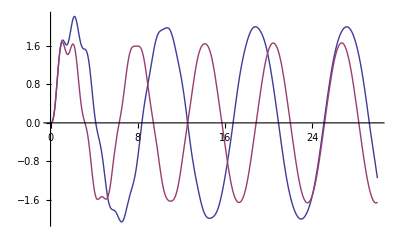

```mathematica
(*C*)
Plot[{nlnsol2,lnsol2},{t,0,30}]
```

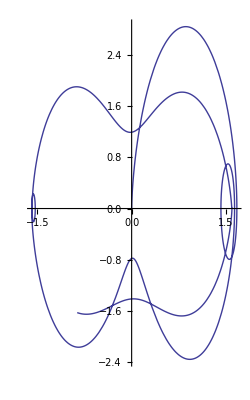

```mathematica
(*Phase Space Plot*)
ParametricPlot[{θ[t],θ'[t]}/.nsol3,{t,0,10},PlotRange->All]
```